# Polypool: Studying infinitely bouncing cue balls in polygons

## Abstract

In this computational essay, I investigated what happened when a cue ball bounced around the interior of a polygon for an arbitrary number of bounces. This data was then combined with image processing techniques to extract insights about the coverings of these polygons and the effect of initial conditions on them.

## 1. Introduction

The polypool process began with creating polygons. Initial tests were ran on random polygons, though as I progressed it became rhombi. In order to implement a bouncing ball, I decided on using a raycasting algorithm (which is elaborated on in depth later) to “bounce” the ball iteratively hundreds or thousands of times. Once we have a plot of those bounces, we can use the image data to gain useful information.

While each section will go more into more detail, I’ll elaborate on the concepts of raycasting here first. Raycasting is an algorithm that originates in 3D computer graphics. The idea is to take a large number of rays and “cast” them at a scene, find where they intersect parts of that scene, and then generate an image based on that. Instead of a scene, we have the sides of a polygon and instead of a pixel we have a bouncing ball.

The analysis part of this essay found in Chapter 2 relies on image processing techniques to quantize the path of that bouncing ball. While the conclusions found in Chapter 2 are certainly interesting, their reliance on black-box image algorithms makes it certainly non-rigorous and everything therein should be taken with a large grain of salt.

## Part One: Polygons

### Initialization

The first task in making Polypool is setting up a bunch of data. For our rhomboids, all we need is a length and two angles.

This is a function that takes an angle and generates a 1x1 rhombus with that interior angle:

```mathematica
genRhombus[angle_]:= CanonicalizePolygon[
Parallelogram[{0,0},{{1,0},AngleVector[angle]}]]
```

Generate a basic rhombus and the position of our starting ray:

```mathematica
rhombusAngle = Pi/7;
poly = genRhombus[rhombusAngle];
initialLength = RandomReal[];
initialAngle = RandomReal[{0,Pi}];
```

### Utility Functions

Before we are able to start casting rays we’re gonna need a lot of geometry. The following functions are all utilities that are necessary to make the main ray algorithm work.

sideList takes the boundary of a polygon and finds the list of Line objects that make up the edges of that polygon from its boundary:

```mathematica
sideList[poly_] := Line /@ Partition[#,2,1]& @ Partition[#,2]& @ (Flatten @ (List @@ RegionBoundary[poly]));
```

This function converts a point in a polygon to the edge of the polygon it resides on:

```mathematica
getCurrentSide[poly_,point_] := Extract[#,{1}]& @ First @ SortBy[RegionDistance[#,point]&] @ sideList[poly];
```

This function converts an array of coordinate pairs to a component form vector, which is necessary for computing collisions later on:

```mathematica
lineToVecRep[line_] := (
line[[2]]-line[[1]]
);
```

This function takes a vector and a pair of coordinate pairs (representing a line) and creates a new vector representing the path of a ball after hitting the side (See Acknowledgements):

```mathematica
calculateNewDirection[originVector_, sideVec_]:= (
Normalize[(2*Projection[originVector,sideVec]-originVector)]
);
```

intersectImproved takes a ray and a line segment and computes the point where they intersect (this is the core of the raycast algorithm, see Acknowledgements):

```mathematica
intersectImproved[ray_, segment_] :=
Module[ {
rx =ray[[1]][[1]],
ry = ray[[1]][[2]],
rdx = ray[[2]][[1]],
rdy = ray[[2]][[2]],
startx = segment[[1]][[1]], 
starty = segment[[1]][[2]], 
endx= segment[[2]][[1]], 
endy = segment[[2]][[2]]},
Quiet @ Solve[t {startx, starty} + (1 - t) {endx, endy} =={rx, ry} + u {rdx, rdy}, {t, u},
Assumptions->0 <= t <= 1 && u > 0
]
]
```

## 2. Pool and Pretty Pictures

## Part Two: The Main Raycasting Algorithm

This section discusses the “main algorithm” that I’ve been referring to in the previous sections of this essay. It is implemented in two functions, castRayPolygon and castRayPolygonNestable. These functions take an abstract representation of a ray and figure out where it will collide with the polygon again. This can be naively iterated over to compute many raycasts, though it is very slow and violates Wolfram Language best practices, so castRayPolygonNestable allows the algorithm to be executed in accordance with the functional paradigm. These functions synthesize all of the previous utilities and data to produce arbitrarily iterated raycasts.

#### detectCollision

The collision detection subroutine used by all the other raycasting algorithms:

```mathematica
detectCollision[ray_,sides_] := Module[{possibleCollisions,dist,pointOfCollision,direction},
direction = ray[[2]];
possibleCollisions =   intersectImproved[ray,#]&  /@ (Sequence @@@sides);
dist = Max @ ((Flatten @ (u /. (possibleCollisions))) /.  u-> -Infinity);
pointOfCollision = startPoint + (dist *direction)
];
```

#### castRayPolygon

castRayPolygon is a function that takes a polygon, a point, and a vector. point represents a point on one line of the polygon and originVector represents the direction of the ray that got us to that point:

```mathematica
castRayPolygon[poly_, point_,originVector_] := Module[{currentSide,ray,sides,collisions,dist,oppRay,newDirection,possibleCollisions,pointOfCollision},
sides = sideList[poly];
currentSide = getCurrentSide[poly,point];
newDirection = calculateNewDirection[originVector,lineToVecRep[currentSide]];
ray = HalfLine[point,newDirection];
pointOfCollision = pointOfCollision = detectCollision[ray,sides];
{pointOfCollision, point,newDirection}
];
```

#### castRayPolygonNestable

This function, while important, is much simpler than castRayPolygon because it just abstracts the logic away from the previous function.

Allows the raycasting algorithm to be Nested:

```mathematica
castRayPolygonNestable[poly_, {point_,originVector_}] := (
	castRayPolygon[poly,point,originVector][[{1,3}]]
);
```

#### generateInitialCast

This function ties together all the initial conditions we set in Part One to “kick off” the actual raycasting. One will notice many similarities with castRayPolygon.

Cast a ray at a given angle at a certain length along one side of a polygon:

```mathematica
(*WARNING: This function assumes it is being computed with respect to the bottom edge of a rhombus, it is NOT a general algorithm and is not guaranteed to work properly otherwise*)
generateInitialCast[poly_, angle_,length_] := Module[{sides,ray,possibleCollisions,dist,pointOfCollision,direction},
sides = sideList @ poly;
startPoint = {sides[[1]][[1]][[1]][[1]]+length,0};
direction = AngleVector[angle];
ray = HalfLine[startPoint, direction];
pointOfCollision = detectCollision[ray,sides];
{startPoint,pointOfCollision-startPoint}
];
```

### And Finally...

We’ve now gotten to the point of finally casting rays and bouncing cueballs.

Initialize an empty list of rays and create a

```mathematica
rays = {};
```

```mathematica
{breakPoint,startDirection} = generateInitialCast[poly, initialAngle,initialLength]
```

{{0.934025,0},{-0.0869182,0.407945}}

```mathematica
castInfo = castRayPolygon[poly, breakPoint, startDirection];
AppendTo[rays,Line[{castInfo[[2]],castInfo[[1]]}]];
```

```mathematica
casts =Nest[c = castRayPolygonNestable[poly,#];AppendTo[rays,Line[{c[[1]],c[[2]]}]]&,{breakPoint,breakPoint-centroid},1000];
```

```mathematica
rayPainting =Rasterize @ Style[Graphics[{Opacity[0.05],rays}],Antialiasing->False]
```

-Graphics-

```mathematica
data = -1*#& @Select[Flatten @Log @ ImageData @ ColorConvert[rayPainting, "Grayscale"],#!=0&];
```

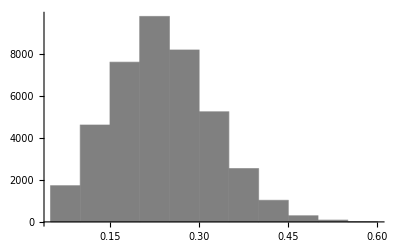

```mathematica
hist = Histogram[data,Automatic,"Count",ChartStyle->Gray]
```

## 3. Conclusions

## Works Cited

https://mathematica.stackexchange.com/questions/26770/getting-rgba-data-from-an-image
https://paulbourke.net/geometry/pointlineplane/

## Acknowledgements